## Section | Dissipative interactions and open quantum systems

This chapter introduces open quantum systems and dissipative dynamics. We contrast unitary evolution of isolated systems with decoherence and loss from environmental coupling, develop the density-matrix and Lindblad master-equation formalisms, and connect them to quantum-jump trajectories. Examples include the decay of coherent states and Schrödinger-cat superpositions and the emergence of statistical mixtures under photon loss.

### Key concepts

Lindblad master equation

Decoherence

Modeling open quantum systems

Workflow for solving master equations

### Quantum jump approach and decoherence

Quantum theory was originally formulated in terms of ensembles because single-system control seemed impossible. In 1975 Dehmelt proposed fluorescence-spectroscopy schemes that required observing individual quantum systems; ion-trap experiments later realized these ideas. The experimental confirmation of discrete quantum jumps helped motivate the quantum-jump (quantum-trajectory) description.

#### Algorithm for general quantum jump

Quantum-jump dynamics provides a Monte Carlo-style unraveling of the master equation. For a cavity at T = 0 K, an emission event corresponds to the loss of one photon, represented by applying the annihilation operator.

Calculate the current probability ΔP of emission of a photon in a time interval δt according to  where is one member of the ensemble

Obtain a random number 0 ≤ r < 1, compare with ΔP to decide emission

Emit if r < ΔP (field loses one photon), the system jumps to renormalized form

No emission r > ΔP, the system evolves according to


where  is the effective non Hermitian Hamiltonian describing non unitary evolution where the second term represents decay of the cavity field.

Iterate the process to record a trajectory of conditional evolution of one member of the ensemble with jump events  t_(1,)t_2...

Average observables over a big number of trajectories to get average behavior or whole ensemble

#### Master equation for density operators

Over a short interval Δt (chosen so that at most one jump occurs), each trajectory branches into two possibilities: a jump with probability ΔP, or no jump with probability 1-ΔP.

For a pure state , the short-time evolution can be written as the weighted sum of the jump and no-jump outcomes:

Averaging over all trajectories (the ensemble) gives:

Taking the limit δt → 0 yields the differential equation:

This is the master equation for the T = 0 K damping problem; it can also be derived by more formal methods.

#### Quantum jumps on familiar states

Assume no coherent interaction (Ĥ = 0), so only dissipation acts. For an initial coherent state |α⟩, the jump operator leaves the state form-invariant because coherent states are eigenstates of the annihilation operator. The no-jump evolution therefore gives:

Set truncation size:

```mathematica
SetFockSpaceSize[20];
```

Effective non-unitary evolution term:

```mathematica
Hdisp = - ⅈ h (γ/2) SuperDagger[a]@a;
```

We verify the no-jump evolution symbolically. The square-root factor in the denominator is only a normalization; in Wolfram QuantumFramework, state equality is understood up to an overall phase and scale.

Symbolic comparison:

```mathematica
MatrixExp[- ⅈ Hdisp /h δt] @ CoherentState[][α]  == CoherentState[][α ⅇ^(-γ δt /2)]
```

True

The state remains coherent, but its amplitude decays exponentially under the non-unitary Hamiltonian.

Non-unitary Hamiltonian:

```mathematica
Hdisp["UnitaryQ"]
```

False

Now consider a cavity field prepared in an even cat state , where 𝒩_e   is the normalization constant. The annihilation operator flips the parity, converting the even cat into an odd cat state.

Photon distribution corresponds to odd cat state after jump:

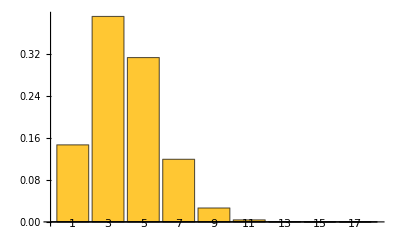

```mathematica
(a @ CatState[][2.,0])["ProbabilityPlot"]
```

For the no-jump branch, the cat amplitude decays; this is sometimes called a "jumping-cat" transition.

We also verify this symbolically without enforcing normalization, so we do not use CatState (which is normalized). Instead we define an unnormalized superposition of coherent states.

Coherent state superposition:

```mathematica
evenCat = QuantumState[CoherentState[][α]+CoherentState[][-α],"Parameters"->α];
```

“No-jump” evolution:

```mathematica
MatrixExp[- ⅈ Hdisp /h δt] @ evenCat  == evenCat[α ⅇ^(-γ δt /2)]
```

True

The cat state shrinks during no-jump evolution (its amplitude decays).

### Decoherence

Decoherence is the gradual conversion of a quantum superposition into a classical statistical mixture due to coupling with an environment. As an example, take an initial even cat state; the joint cavity-environment state is:

where |ϵ⟩ denotes the environment state. The environment can include many degrees of freedom, but we do not need to model them explicitly. At a later time the joint state evolves to:

such that  from the previous section, so the field becomes entangled with the environment. If we compute the density operator and trace over a complete set of environment states , we obtain the reduced field density operator:

which is a statistical mixture of two coherent states.

### Dissipative interactions from master equations

#### Dissipation of a coherent state

```mathematica
SetFockSpaceSize[15];
```

Set initial parameters for a coherent state |α⟩ with |α| = 2:

```mathematica
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
ρ0=coherent[αcoh];
```

Establishing a damping parameter:

```mathematica
γ = RandomReal[{1,2}];
```

Set up the Liouvillian master equation with Ĥ= (â)^†â and L_1=â:

```mathematica
ℒ= QuantumOperator["Liouvillian"[SuperDagger[a]@a,{a},{γ}]];
```

ℒ is a superoperator:

```mathematica
ℒ["Type"]
```

Superoperator

Compute the evolution numerically (include ⅈ when evolving with a superoperator):

```mathematica
ρt=QuantumEvolve[ⅈ ℒ,ρ0,{t,0,1}];
```

Define helper variables for the evolution statistics:

```mathematica
time=Range[0,1,0.01];
fock=Range[$FockSize]-1;
```

Compute the mean photon number and the fidelity relative to the analytical solution (which remains a coherent state):

```mathematica
qs=QuantumSimilarity[coherent[αcoh ⅇ^(-ⅈ #) ⅇ^(-1/2 # γ)],ρt[#]]&/@time;
meanN=Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]&/@time;
```

Plot the statistics; the numerical state follows the analytical exponential decay of the mean photon number:

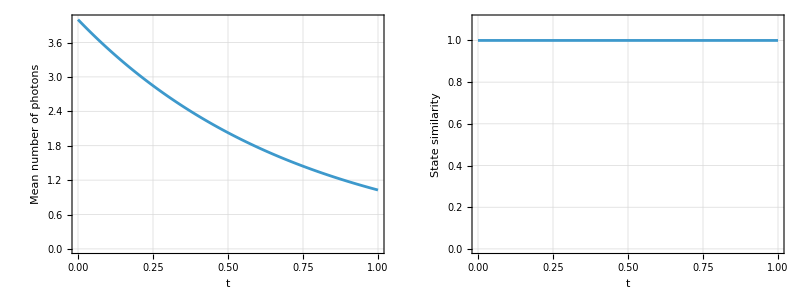
-Graphics-Evolution statistics of a coherent state

```mathematica
Labeled[Grid[{{ListLinePlot[Thread[{time,meanN}],],ListLinePlot[Thread[{time,qs}],]}}],]
```

|α|^2 ⅇ^(-γ t) is the expected mean photon number. The corresponding energy decay time is

Do an exponential decaying fit:

```mathematica
nlm =NonlinearModelFit[Thread[{time,meanN}],k Exp[-g t],{k,g},{t}];
```

Fitted decay law:

```mathematica
nlm["Function"][t]
```

3.99977 ⅇ^(-1.35942 t)

Compare the parameters:

```mathematica
(g /. nlm["BestFitParameters"]) - γ
```

1.11973×10^-8

The Wigner function shows a spiral: the unit-frequency Hamiltonian rotates the coherent state while dissipation pulls it toward the origin:

-Graphics-

#### Decoherence of an even cat : becoming statistical mixture

```mathematica
SetFockSpaceSize[15];
```

Now analyze the evolution of a cavity prepared in an even cat state:

```mathematica
αcoh = 2*Exp[I RandomReal[{0,2Pi}]];
ρ0 = CatState[][αcoh,0];
```

Setting a pure decoherence master equation with photon loss (H = 0):

```mathematica
γ = 0.9;
ℒ= QuantumOperator["Liouvillian"[None,{a},{γ}]];
```

Evolve the state:

```mathematica
ρt = QuantumEvolve[ⅈ ℒ, ρ0, {t,0,10}];
```

Monitor the trace and purity. is related to the purity and also  is a measure of decoherence. At long times the purity increases again because energy loss drives the state toward the vacuum (a pure state):

Sampling time:

```mathematica
time=Range[0,10,0.01];
```

Compute trace and purity:

```mathematica
traces = Table[{Tr[ρt[t]],ρt[t]["Purity"]},{t,time}];
```

Plot result:

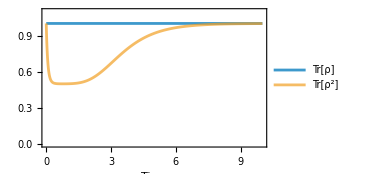

```mathematica
ListLinePlot[Thread[{time,#}]&/@Transpose[traces]
,]
```

The energy decay (mean photon number) still falls exponentially, as expected:

```mathematica
meanPhotons = Table[{t,Dot[fock,Diagonal[ρt[t]["DensityMatrix"]]]},{t,time}] ;
```

Plot the curve:

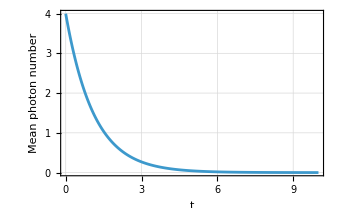

```mathematica
ListLinePlot[meanPhotons,]
```

The analytical solution of the master equation is:

Implement analytical solution:

```mathematica
sol =QuantumState[coherent[αcoh ⅇ^(-γ  t/2)]["MatrixState"]+coherent[-αcoh ⅇ^(-γ  t/2)]["MatrixState"]+ QuantumOperator[ⅇ^(-2 Abs[αcoh]^2(1-ⅇ^(-γ t)))(coherent[αcoh ⅇ^(-γ  t/2)]@SuperDagger[coherent[-αcoh ⅇ^(-γ t /2)]]+coherent[-αcoh ⅇ^(-γ  t/2)]@SuperDagger[coherent[αcoh ⅇ^(-γ t /2)]])]["MatrixQuantumState"],"Parameters"->t]["Normalize"];
```

Compute fidelity as function of time:

```mathematica
AbsoluteTiming[similarities = Table[QuantumSimilarity[ρt[t],sol[t]],{t,0,10,0.05}];]
```

{28.5655,Null}

Verify that the numerical and analytical states agree (similarity is approximately 1 up to numerical error):

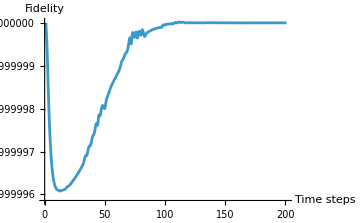

```mathematica
ListLinePlot[similarities,]
```

Apart from the energy decay, the analytical solution contains an extra factor  that multiplies the "coherences" (off-diagonal elements). For short times, a decoherence time follows from the expansion . This implies  as long as .

This is visualized with the Wigner representation by choosing a time between T_decay and T_decoh:

```mathematica
Tevol = 1/(2γ);
```

Statistical mixture of coherent states (for comparison):

```mathematica
ρmix = 1/2(coherent[αcoh]["MatrixState"]+coherent[-αcoh]["MatrixState"]);
```

Plot the Wigner function:

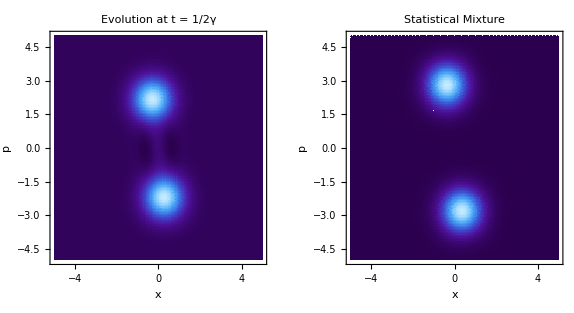

```mathematica
GraphicsRow[Table[wig = WignerRepresentation[s[[1]],{-5,5},{-5,5}];DensityPlot[wig[x,p],{x,-5,5},{p,-5,5},],{s,{{ρt[Tevol],"Evolution at t = 1/2γ"},{ρmix,"Statistical Mixture"}}}],Spacings->20]
```

This confirms that the coherences decay faster than the energy, so the evolved state becomes a statistical mixture. The amplitudes are reduced because photon loss acts during the evolution.

After sufficiently long times, photon loss drives the state to the vacuum:

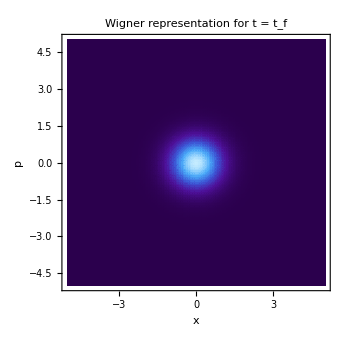

```mathematica
wig = WignerRepresentation[ρt[10.],{-5,5},{-5,5}]; DensityPlot[Chop@wig[x,p],{x,-5,5},{p,-5,5},]
```

### Generation of coherent states from decoherence: optical balance

Dissipation typically destroys coherence in superpositions. However, appropriately engineered dissipation can also generate coherence. The master equation contains unitary (commutator) and non-unitary (dissipative) terms, and their nonlinear interplay can balance so that the long-time state (t → ∞) is not the vacuum.

Consider the interaction Hamiltonian OverHat[H_I] = h G(â+(â)^†) , where G is the strength of a classical pump propagating through an absorbing medium. The master equation becomes:

Start from a random cavity field:

```mathematica
ρ0 = QuantumState["RandomPure",$FockSize]
```

QuantumState[…]

Set simulation parameters, driving strength, and photon-loss rate:

```mathematica
G = RandomReal[{1,2}];
γ  = RandomReal[{1.5,2}];
```

Define the Liouvillian, now including the driving term Ĥ≠ 0:

```mathematica
ℒ= QuantumOperator["Liouvillian"[G(a+SuperDagger[a]),{a},{γ}]];
```

Solve the master equation numerically:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,ρ0,{t,0,3}];
```

The steady-state solution converges to ρ = |β⟩⟨β|, where β = - 2 ⅈ G/γ:

```mathematica
similarities= Table[{t,QuantumSimilarity[ρt[t],coherent[-I 2G/γ]]},{t,0,3,0.1}];
```

Plot state-fidelity, we see it approaches 1 as time evolves:

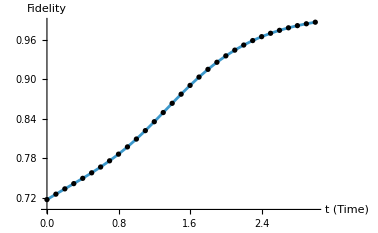

```mathematica
ListLinePlot[similarities,]
```

If we start from the vacuum state ρ̂(0) = |0⟩⟨0| and focus on short times, we can neglect dissipation. The evolution is then unitary and produces a coherent state of the form | -ⅈ G t ⟩⟨- ⅈ G t |, independent of γ. The fidelity stays near 1 until this approximation breaks down.

Evolve the ground state:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,FockState[0],{t,0,3}];
```

Auxiliary variables for time steps and Fock numbers:

```mathematica
time = Range[0,0.8,0.02];
fock =Range[$FockSize]-1;
```

Computing fidelity and mean photon number:

```mathematica
qs = QuantumSimilarity[coherent[-I G #],ρt[#]]& /@ time;
meanN = Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

Plot the statistics:

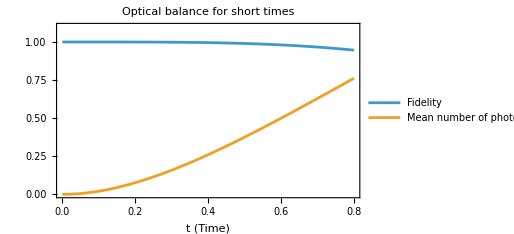

```mathematica
ListLinePlot[Thread[{time,#}]&/@{qs,meanN},]
```

### Thermalization master equation

Master equation:

where n_th is the thermal mean photon number (set by temperature and cavity frequency) and κ is the photon-loss rate.

Set up truncation size:

```mathematica
SetFockSpaceSize[25];
```

Final evolution time:

```mathematica
tf = 10.;
```

Implement the master equation (Ĥ=ℏ ω a^†a) with the relevant jump operators:

```mathematica
ℒ = QuantumOperator["Liouvillian"[ ω SuperDagger[a]@a,{a,SuperDagger[a]},{κ(nth+1),κ nth}],"Parameters"->{ω,κ,nth}];
```

Pick some parameters, for example n_th = 3, ω = 1, κ = 0.6 :

```mathematica
liouville =ℒ[1,0.6,3];
```

Calculating mean number of photons for different initial Fock states:

```mathematica
meanPhotons =
Table[ρt = QuantumEvolve[ⅈ liouville ,FockState[i],{t,0,tf}];Table[{t,Dot[Range[0,$FockSize-1],Diagonal[ρt[t]["DensityMatrix"]]]},{t,0,tf,0.01}],{i,{0,1,4}}];
```

Plot the mean photon number and compare with n_th:

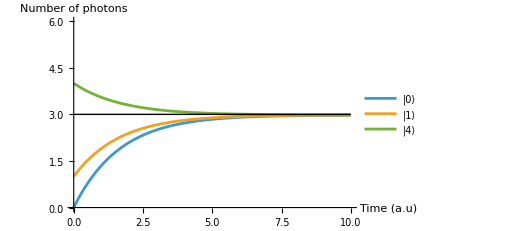

```mathematica
ListLinePlot[meanPhotons,]
```

It converges to a thermal state with mean photon number n_th:

```mathematica
QuantumSimilarity[ρt[tf],ThermalState[3.]]
```

0.999624

Change the κ parameter and compute the evolved states:

```mathematica
evolved =Table[QuantumEvolve[ⅈ ℒ[1,k,3],FockState[0],{t,0,tf}],{k,{0.5,1.,1.5}}];
```

Calculate again the mean number of photons:

```mathematica
meanPhotons =Table[{t,Dot[Range[0,$FockSize-1],Diagonal[#[t]["DensityMatrix"]]]},{t,0,tf,0.01}]&/@evolved;
```

Plot the curves, we see change in the rate of convergence such that higher κ converges faster:

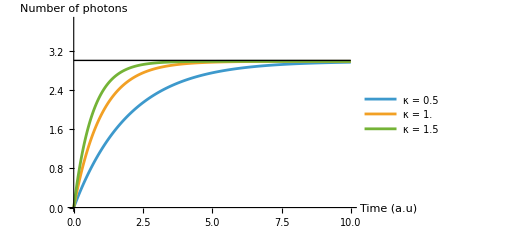

```mathematica
ListLinePlot[meanPhotons,]
```

### Jaynes-Cummings with dissipation

We revisit the Jaynes-Cummings model, now including jump operators for energy dissipation. The master equation is:

The jump operators are L_decay=√γ_1(σ_- ⊗ ℐ) and L_loss = √γ_2(ℐ ⊗ a), associated with dissipation rates γ_1 and γ_2 for atomic decay and photon loss, respectively.

Annihilation operator acting on the second qudit:

```mathematica
a:= AnnihilationOperator[{2}];
```

Atomic raising and lowering operators:

```mathematica
atomBasis = QuantumBasis[{"e","g"}];
σplus = QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];
```

Set field frequency, atomic frequency, and coupling; we consider the resonant case (ν = ω):

```mathematica
SetFockSpaceSize[8];
ν = 10.;   (* field frequency *)
ω = 10.;   (* atomic frequency *)
gc = 15.; (* interaction coupling strength *)
```

Consider the initial state |e⟩ |n⟩ with n = 2:

```mathematica
ψ0 = QuantumState["0",atomBasis]//FockState[2]
```

e2

Jaynes-Cummings Hamiltonian:

```mathematica
H =  ν SuperDagger[a]@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@SuperDagger[a]);
```

Jump operators:

```mathematica
decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;
```

Compute the probability of finding the atom in the excited state:

```mathematica
atomProb[evolved_,tspecs_] := Table[{t, (SuperDagger[QuantumState["0",atomBasis]]@evolved[t])["Norm"]}, Evaluate[{t, Sequence@@tspecs}]]
```

Calculate the evolution for several damping parameters with γ_1=γ_2, and record the excited-state probability. QuantumOperator also accepts the "Hamiltonian" syntax to include jump operators; when using QuantumEvolve you do not need an extra ⅈ in this case.

```mathematica
probsE = Table[ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {x, x}]];
   evolved = QuantumEvolve[ℋ, ψ0, {t, 0, 2}];
   atomProb[evolved,{0,2,0.01}],
   {x, {0.8, 0.4, 0.2}}];
```

Damped Rabi oscillations:

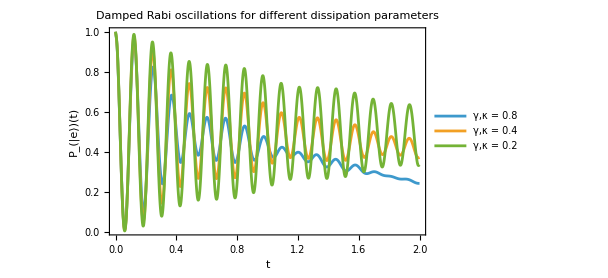

```mathematica
ListLinePlot[probsE,]
```

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"];
```

Exercises

What jump operator do you think represents dephasing for a bosonic mode? Generate an animation of the evolution of the density matrix of a uniform superposition state, under the dephasing channel (with  H=0)

Solution

Generate a uniform superposition state:

ρ = QuantumState["UniformSuperposition",$FockSize]

Dephasing can be modelled with the jump operator a^†a:

ℒ = QuantumOperator["Liouvillian"[ None,{(a^†)@a},{κϕ}],"Parameters"->{κϕ}];

Evolution of the state:

evolved =QuantumEvolve[ⅈ ℒ[0.2], ρ,{t,0,10}];

Get frames:

frames = Table[MatrixPlot[evolved[t]["DensityMatrix"],ColorFunction->"RedBlueTones",PlotLegends->All, PlotLabel->StringForm["t = ``",Round[t,0.01]],ImageSize->300,ImageMargins->20,LabelStyle->13],{t,10^-6,5,0.1}];

Export the GIF:

Export[NotebookDirectory[]<>"Dephasing.GIF",frames,"GIF","DisplayDurations"->Reverse@Subdivide[0.1,0.5,Length[frames]-1]];

Energy exchange between cavities (allowing decay) can be modelled with the jump operator (μ a_1 - λ a_2^†), where μ and λ are parameters. Consider an initial state |1,1⟩ and μ>λ. How does the entanglement of the two mode system behaves as function of time?

Solution

Set the size of the Fock space:

SetFockSpaceSize[10];

Operators of the two modes:

{a,b}=Array[AnnihilationOperator[{#}]&,2];

Initial state:

ρ0 = FockState[{1,1}];

Setting μ and λ:

{μ,λ}={0.6,0.2};

Build Liouvillian with jump operator μ a - λ b^†:

ℒ =QuantumOperator["Liouvillian"[None,{μ a - λ b^†},{0.6}]];

Evolve the state:

evolved = QuantumEvolve[ⅈ ℒ,ρ0,{t,0,4}]//Quiet;

Plot the measure of entanglement:

ListLinePlot[Table[QuantumEntanglementMonotone[evolved[t],{{1},{2}},"LogNegativity"],{t,0,4,0.1}],DataRange->{0,4},AxesLabel->{"t","LogNegativity"},PlotRange->All]

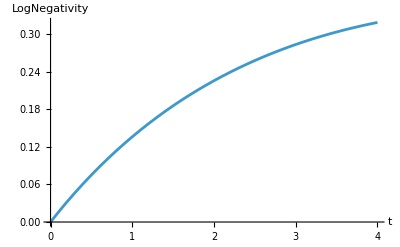

In the last section we saw the dissipative Jaynes-Cummings with a Fock state, now observe how collapse and revivals change with dissipation. The point of this exercise is to encourage exploration and determine relevant parameters. There are different regimes of interaction, so changing the Hamiltonian parameters and the γ rates can result in diverse dynamics.

Solution

Set the truncation size and relevant parameters:

SetFockSpaceSize[20];
ν = 8.;   
ω = 8.;   
gc = 10.; 
γ1 = 0.5;
γ2 = 0.5;

Hamiltonian:

H =  ν a^†@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@a^†);

Master equation set up:

decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;

ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {γ1, γ2}]];

Evolution:

evolved = QuantumEvolve[ℋ, QuantumState["1",atomBasis]//coherent[3.],{t,0,10}];

Plotting results:

probs = atomProb[evolved,{0,10,0.1}];
ListLinePlot[probs,InterpolationOrder->2,PlotRange->All,PlotStyle->Red]

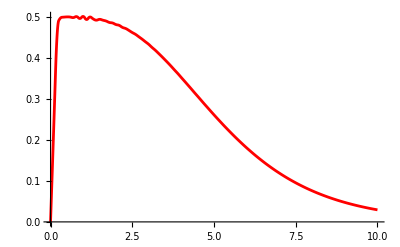

Comparing with the case without dissipation, already with γ_1=γ_2=0.5 all oscillations disappear:

Show[%326,%356]